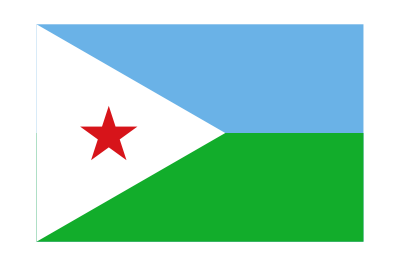
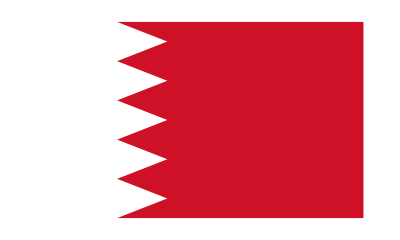
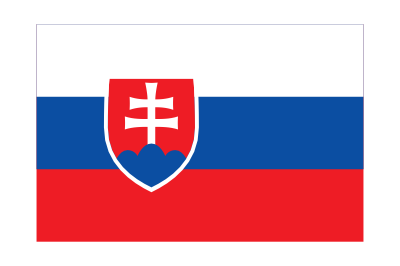
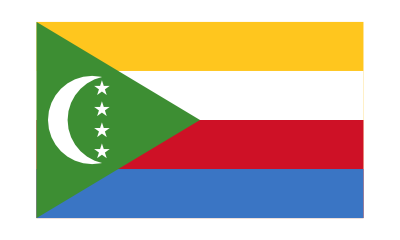
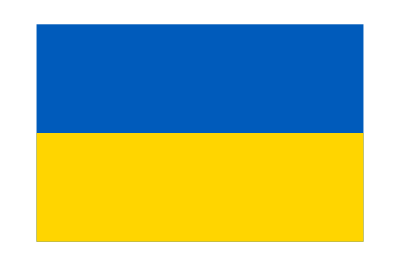
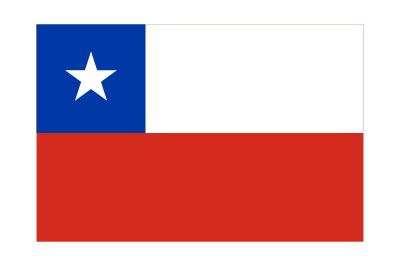
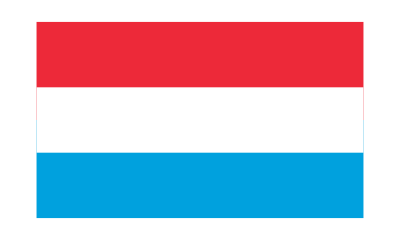
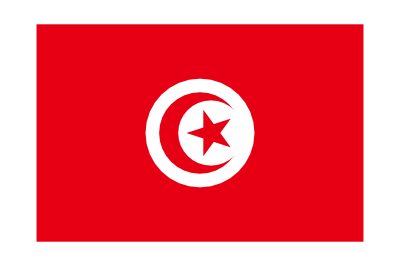

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
flag=DeleteMissing[EntityValue[RandomSample[EntityList[EntityClass["Country","Countries"]],150],"Flag"]]
```

```mathematica
flagcolours=Flatten[DominantColors[flag]](*Unpack nested list*)
```

{RGBColor[0.0003492278714192132, 0.4705904508760866, 0.3686360091096576],RGBColor[0.9965087405505838, 0.9978830390718508, 0.9976015939744974],RGBColor[9.6950303584864*^-7, 0.14874677776394074, 0.391882454116325],RGBColor[0.7764714955457706, 0.04705020633819205, 0.18823549991372052],RGBColor[0.9960793101246584, 0.7960776260261124, 2.279485423703487*^-6],RGBColor[0., 0.3213745212055998, 0.576372480036106],RGBColor[0.9960793101246584, 0.7960776260261124, 2.279485423703487*^-6],RGBColor[0.9919750872057796, 0.7253065644332934, 0.07433083273773244],RGBColor[0., 0.4156862928784661, 0.26666636987219783],RGBColor[0.7568636240825978, 0.15293816722141823, 0.17647080911413301],RGBColor[0.000043048603847383735, 0.1372913744483464, 0.584327298903301],RGBColor[0.9989042266441058, 0.9990016252442006, 0.9994919731989212],RGBColor[0.9294128488591151, 0.1607797979138483, 0.22352970228560526],RGBColor[0.9999632620415845, 0.9999206676731939, 0.9997615361604425],RGBColor[0., 0.3999386138493647, 0.],RGBColor[0.8000009919470249, 0., 1.722145900004482*^-6],RGBColor[0.972581102861393, 0.7718992093191122, 0.040892218432522866],RGBColor[0.8078064187944697, 0.0666603824514243, 0.14902764641238353],RGBColor[0.0003017614938754188, 0.00024003679322757513, 0.000012215974698533676],RGBColor[0.005525145007749403, 0.4459343705847422, 0.7746168791446381],RGBColor[0.9856813626196143, 0.9902262002381573, 0.995098334007766],RGBColor[0.9865665922004253, 0.8181462206264276, 0.08585267967883078],RGBColor[0.13334808350206057, 0.35847634090827907, 0.19967225579821019],RGBColor[0.00015485009175253084, 0.3177455002581522, 0.7294394085023481],RGBColor[0.9881675276671001, 0.8195728388143703, 0.08630127899488921],RGBColor[0.9944045488615582, 0.9958613799364134, 0.9978303400364633],RGBColor[0., 0.5956447986155141, 0.7644892204301632],RGBColor[0., 0.682352960154769, 0.39607798634814384],RGBColor[0.8784406320937558, 0.00007813615617875162, 0.20399081913518585],RGBColor[0.999304455906031, 0.9977294164854585, 0.9980102775693515],RGBColor[1., 0.599826167109708, 0.1998290243303119],RGBColor[0.07058568120922368, 0.5333333116050757, 0.027450682605582036],RGBColor[0.9998697699785232, 0.9998688468893541, 0.9999283536557996],RGBColor[0.5062041290752936, 0.5060647583014052, 0.7668453122329381],RGBColor[0.0273528299372544, 0.53705485840263, 0.18807794946916345],RGBColor[0.9878048568156842, 0.8663754062848406, 0.035168339028901215],RGBColor[0.8547546531695723, 0.07244248040556847, 0.10171715974959641],RGBColor[0.07035120818000781, 0.6783109479496213, 0.1685071596646899],RGBColor[0.9998178121474842, 0.8076845172155815, 2.1290102909088394*^-6],RGBColor[0.8235303759638943, 0.06273708689509525, 0.20392178275541173],RGBColor[0.003381735770866517, 0.002596018135134542, 5.897017595743535*^-8],RGBColor[0.286272790773112, 0.5921569212382556, 0.8156854633322589],RGBColor[0.9996830159493416, 0.9997140662249727, 0.9996752331575846],RGBColor[0.14475853027972205, 0.26060051326366757, 0.05854851233339859],RGBColor[0.9147907315604509, 0.8485988975687226, 0.539302708453598],RGBColor[0.9803928902040676, 0.878430671715865, 0.2588236156468351],RGBColor[0.9293667102307084, 0.16073393124169455, 0.22348355249142554],RGBColor[6.636694485562685*^-8, 6.636686583450336*^-8, 6.636681958909097*^-8],RGBColor[0.1918822272552763, 0.5719851318932588, 0.03060905274586604],RGBColor[0.9999131329217669, 0.8234524332997, 2.232182935096305*^-6],RGBColor[0.8702029016398234, 0.12568641063097927, 0.06281424723112491],RGBColor[0.9984830877655971, 0.9983419285884493, 0.9983132761646142],RGBColor[0.005664550210263369, 0.0022789665602901783, 0.0008993224381382817],RGBColor[0.000040233106717870725, 0.21932416922751158, 0.658522557070885],RGBColor[0.8078532842763554, 0.0667354866371436, 0.14908097802988404],RGBColor[0.9994480619441967, 0.9992527785025903, 0.9990230214286776],RGBColor[0.9882411017952116, 0.8204940092963731, 0.09348412366743555],RGBColor[0.8075914207440076, 0.06653472760743392, 0.14876960963559113],RGBColor[0.00006883682606589531, 0.15691981363041813, 0.4078785039651841],RGBColor[0.9994410455139163, 0.9994950474024095, 0.9996327124879577],RGBColor[0.929366710230708, 0.16073393124169547, 0.22348355249142549],RGBColor[0., 0.1372553047428195, 0.584313134695112],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0.2547781768297804, 0.5368771832010286, 0.8665860310484643],RGBColor[0.975000745406467, 0.8387252528477386, 0.08729370579065288],RGBColor[0.8238917215934918, 0.0657139946550667, 0.20604590068009127],RGBColor[0., 0.16848924534440043, 0.4979012638388472],RGBColor[0.8077517810300169, 0.0666135042814934, 0.14892799694167397],RGBColor[0.9881437985538634, 0.8195609246315, 0.08618596661613406],RGBColor[0.0012080729749375213, 0.4788353021340828, 0.302216928525434],RGBColor[0.1071425432397333, 0.13837569106843206, 0.572280066755303],RGBColor[0.8705892609062291, 0.2196050323080488, 0.19215719069713638],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0.0007009596012018557, 0.000494559252622942, 6.497269309016713*^-8],RGBColor[0.9993837203109582, 0.7131071045024473, 0.07038483776802379],RGBColor[0.9684251625777364, 0.8780637522157521, 0.09078678615703997],RGBColor[0.9998218784812555, 0.9996423049278454, 0.9994706112497117],RGBColor[0.00043317343538136905, 0.0000833706604384643, 0.0000401754210253437],RGBColor[0.812946632102308, 0.08195460227465848, 0.14796854950650404],RGBColor[0.000017437145477244288, 0.14100222206400864, 0.4900921542653392],RGBColor[0.8122295388157218, 0.08143135608193239, 0.17092922088301635],RGBColor[0.9970306957656864, 0.99429526627573, 0.9950387836529223],RGBColor[1., 0.6037318203555465, 0.009907457685817496],RGBColor[0.8076333922030238, 0.06687188783302417, 0.14872501502532182],RGBColor[0.00017722815427646777, 0.0001568212564015245, 5.635274101852984*^-6],RGBColor[0.9742342112560026, 0.8363884407345407, 0.08594547980341657],RGBColor[0.45469288439482597, 0.6743014378432277, 0.8744049143276726],RGBColor[0.9923462159778308, 0.9951903114562123, 0.9978235151568485],RGBColor[0.8660914132802858, 0.7106206685498397, 0.48123149136971183],RGBColor[0.9583319536704532, 0.6986866875849318, 0.052628491969833956],RGBColor[0.2155351346439618, 0.49382102372459663, 0.246907959512978],RGBColor[0.7059388812096685, 0.03949777487553152, 0.17644091671339682],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0.9250870429963807, 0.7831314691666449, 0.11372875530949297],RGBColor[0., 0.6076905626320079, 0.28204820349945525],RGBColor[0.9993242546759834, 0.9996788540672755, 0.9993525697514255],RGBColor[1., 0.4744471164634408, 2.6586664119526705*^-6],RGBColor[0.9294131492429938, 0.10990897582627354, 0.15303984255093803],RGBColor[0.00783484399685854, 0.309585069308216, 0.6348626792487924],RGBColor[0.8117195301506958, 0.07833546776318995, 0.16858162314149025],RGBColor[0.9999994990303583, 0.9999925594146056, 0.9999929194100564],RGBColor[0.7111171097107978, 0.7058804774923308, 0.702125647926626],RGBColor[0.000012769309737687556, 0.41947806132545634, 0.24693102386975213],RGBColor[6.636694485562685*^-8, 6.636686583450336*^-8, 6.636681958909097*^-8],RGBColor[0.9625107476796343, 0.807007570621283, 0.08932306817107233],RGBColor[0.8286784589181886, 0.10982296670584474, 0.18734730795852017],RGBColor[0.9999400245598814, 0.9997693496032297, 0.9997994187333753],RGBColor[0.14117629156712297, 0.11372548255650053, 0.3098036039165395],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0.929235962746172, 0.10945387285760327, 0.14082765724065965],RGBColor[0.807502571867773, 0.06649100292869015, 0.14868171200969504],RGBColor[0.0008647219454652603, 0.000864720474440924, 0.0008647197015336935],RGBColor[0.9996691080279457, 0.9997964572386372, 0.999720401506699],RGBColor[0.0065739595706691, 0.4816414750181868, 0.24379413994492877],RGBColor[0.5305402057576831, 0.7532013652912722, 0.6407718178274102],RGBColor[6.636694485562685*^-8, 6.636686583450336*^-8, 6.636681958909097*^-8],RGBColor[0.8078440877821454, 0.06665926215587997, 0.14902001662945386],RGBColor[0.9998341791090054, 0.9998975630091199, 0.9998590055073416],RGBColor[0.00948652345949796, 0.48314006001453097, 0.24635292787030516],RGBColor[0.8117157898647737, 0.07840508441328653, 0.16856217162960777],RGBColor[0.00015389902940202705, 0.1412757352732655, 0.49021204675068347],RGBColor[0.9998774385577943, 0.7998911285923856, 2.227158941895402*^-6],RGBColor[0.290008629459936, 0.6783332990209167, 0.8390081345431907],RGBColor[0.9997137840148481, 0.8704800868989788, 0.0002742472410533225],RGBColor[0.000012649447245888789, 0.21940521199914736, 0.576353356709937],RGBColor[0.9974054030764131, 0.9976675208424829, 0.9985399552238386],RGBColor[0.8078689305792152, 0.06684434199276112, 0.1489728438320162],RGBColor[0.00003567836945439162, 0.14114741470149786, 0.4901844509619809],RGBColor[0.8115278988906924, 0.07850258656944481, 0.1686830421623259],RGBColor[0.9950053097470429, 0.9913431613266718, 0.9931199938391359],RGBColor[0.9999746108632309, 0.9999074444003825, 0.9999192813842418],RGBColor[0.8156979971364967, 0.04715105032585675, 0.20007592478231312],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0.004543874893284347, 0.5897968662236367, 0.4335520408536162],RGBColor[0.8392166804937593, 0.1490156492070002, 0.07058936084511166],RGBColor[0.00011298903449266428, 0.14107070587215523, 0.4901510607091209],RGBColor[0.9945681218737955, 0.9921903820246999, 0.9940027982759682],RGBColor[0.8117656643174511, 0.07842481107254418, 0.16862778380596863],RGBColor[0.8391824819816179, 0.15727776148845568, 0.15685545715581753],RGBColor[0.9997310764254616, 0.9998095409545346, 0.9997457003523255],RGBColor[0.9878594442270175, 0.8467406269185097, 0.3371899796467193],RGBColor[0.0002541796011587166, 0.24724267061560662, 0.5293503220111205],RGBColor[0.00033426752002162956, 0.4785892387262198, 0.23943672378761027],RGBColor[0.00005798816632263171, 0.14094832519755676, 0.49005471415640517],RGBColor[0.9956370339709365, 0.8192659865779268, 0.00018590470476022414],RGBColor[0., 0.5999538251293277, 0.],RGBColor[6.636694485562685*^-8, 6.636686583450336*^-8, 6.636681958909097*^-8],RGBColor[0.7490231871691401, 0.0018833448870497651, 0.0008671144938852183],RGBColor[0.8215342460361179, 0.43573168309723476, 0.3240943252976935],RGBColor[0.8078578438920686, 0.06677665398302862, 0.14911128215711297],RGBColor[0.9999473889574902, 0.9998099246386508, 0.9998243675565032],RGBColor[0.00018798635493876448, 0.6194633492961934, 0.2862951206147467],RGBColor[0.7983609700534929, 0.07897300665754617, 0.14869156769586722],RGBColor[0.9878290077095798, 0.8194149235979444, 0.08753559364794508],RGBColor[0.997888364795159, 0.9986178002348199, 0.9971624760597134],RGBColor[0.003488720423739053, 0.00288613005082627, 0.001652273835495517],RGBColor[8.96764281617557*^-6, 0.14117535050206714, 0.490173091574398],RGBColor[0.9956859106979589, 0.9925422101745224, 0.9938883113187263],RGBColor[0.813265727967922, 0.09564446720570058, 0.17842736959046301],RGBColor[0.008131424851873178, 0.010643679778521714, 0.00730176301345077],RGBColor[0., 0.37142179674870335, 0.1561598113282922],RGBColor[0.9999763848290922, 0.999930436772927, 0.9999353515523847],RGBColor[0.737308321367562, 0.0002364930826611737, 0.17665857373579413],RGBColor[0.999892952855176, 0.9998922051154732, 0.999891812239294],RGBColor[0.3684580626242338, 0.713437156836921, 0.89376517194841],RGBColor[0.5241655186160314, 0.5281628544130488, 0.5282814486482655],RGBColor[0.5316422762253287, 0.40871715228042393, 0.11663702595062686],RGBColor[0.3285850555895716, 0.45899164669047793, 0.29763700843291135],RGBColor[0.25618643979096767, 0.2848251571615714, 0.2362541604525928],RGBColor[0.8547391648300002, 0.14505931649791184, 0.11363067089843928],RGBColor[0.9997222625722403, 0.9992704995891847, 1.0341887716447395*^-6],RGBColor[0., 0.6196078655190792, 0.37647016028617836],RGBColor[0.9882361169657891, 0.8196070649226719, 0.08627563102141758],RGBColor[0.22738029362212808, 0.4587889285787205, 0.7685572348542468],RGBColor[0.929366710230708, 0.16073393124169547, 0.22348355249142549],RGBColor[0., 0.1372553047428195, 0.584313134695112],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0.9879937511584084, 0.8194845032559722, 0.08604009259428319],RGBColor[0., 0.2195468485623006, 0.5764393975604079],RGBColor[0.8077827902371013, 0.06662887703841477, 0.1489589104284144],RGBColor[0.9998836986100049, 0.9997984463858921, 0.9998358408848217],RGBColor[0.823536325337621, 0.06281359476605905, 0.20397905229674618],RGBColor[0.0001681455272561938, 0.32168223665704854, 0.5765329002508415],RGBColor[0.11731299078728144, 0.7096320084235529, 0.22711334493293006],RGBColor[0.0008267243799327084, 0.4475544399486488, 0.7766888183355546],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0.0005993616006293776, 0.6195232109809162, 0.28574930129675363],RGBColor[0.0007594928317427272, 0.0007147534693465659, 0.00035174075465130506],RGBColor[0.8079269016435976, 0.06725843030152684, 0.14898036033911538],RGBColor[0.9871009365786704, 0.8185146871516543, 0.08601408724540793],RGBColor[0.9966267961279599, 0.9966260507034076, 0.9966256590436505],RGBColor[0.8075006408882642, 0.0671626855582215, 0.1485051567041436],RGBColor[0.9879265156822984, 0.8191951296215876, 0.08630954885397615],RGBColor[0.00040104072416455777, 0.47846741184935565, 0.36846981390190536],RGBColor[4.989659377454547*^-6, 0.4979383582703362, 0.9999757324921171],RGBColor[0.8079427201005847, 0.0634020947029707, 0.12931578585882247],RGBColor[0.9673449927985697, 0.8374987127062529, 0.09487803256838087],RGBColor[0.000025685265135477198, 0.1410415452870963, 0.49006191261341564],RGBColor[0.9931308108527998, 0.9920825318215999, 0.9939750201375929],RGBColor[0.8126915013752656, 0.08431015260614247, 0.1727682480961651],RGBColor[0.0032147266486326474, 0.44366218069037067, 0.7626694252957509],RGBColor[0.00017021261419075228, 0.00015753209755096272, 0.5450765974841429],RGBColor[0.9947505558330826, 0.993711908941385, 0.9960796740067354],RGBColor[1., 0.01687909417355233, 0.014223891799763468],RGBColor[0.9957316118172027, 0.7959327136454106, 0.00019669236250846101],RGBColor[0.9175841378026846, 0.15686998485951714, 0.2235637375434827],RGBColor[0.20616581313651527, 0.6982699735873145, 0.19988179548026486],RGBColor[0.9995520259931049, 0.9995611670866665, 0.9993340034674173],RGBColor[0.8704298799389418, 0.16070119925458973, 0.0625909105200721],RGBColor[1., 0.8705874779106686, 1.9955386367809247*^-6],RGBColor[0.8007068456598315, 0.005940721832894113, 0.00872598585652821],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0.003949538205250355, 0.00002906854271901625, 0.3999685344896707],RGBColor[0.9583639221210628, 0.7831584377798577, 0.7815578725983277],RGBColor[0.998158627670389, 0.7983197209666681, 0.000558702757830416],RGBColor[0.9990184966294539, 0.9991565886411261, 0.999509027763065],RGBColor[6.903831489967205*^-6, 0.2078505115904738, 0.5019644273133114],RGBColor[0., 0.5722772404715953, 0.2742367566148468],RGBColor[0.8077517269172869, 0.16857818573308309, 0.2156402328051123],RGBColor[1., 0.9999994542921625, 0.9999990613760404],RGBColor[0.000011600240224607107, 6.618318575800648*^-8, 6.620121100307991*^-8],RGBColor[0.0009749081542770905, 0.4789140187868231, 0.24003006989927939],RGBColor[0.999985894778522, 0.9999645447131406, 0.9999641379326331],RGBColor[0.8077583082728241, 0.06665986710600003, 0.1490200862985731],RGBColor[0.9998963296371816, 0.9999163357557243, 0.9999367551771948],RGBColor[0.843055134998585, 0.07842429832536602, 0.10198291325802572],RGBColor[0.0669020677201311, 0.27065124238128785, 0.4941170221564842],RGBColor[0.8076653478976507, 0.0666700182535695, 0.1489154568564978],RGBColor[0.0008529685857627408, 0.0008529671347332931, 0.000852966372331743],RGBColor[0.9982717632146764, 0.997798011203585, 0.9978379580436049],RGBColor[0.8076003215694151, 0.06653910746201458, 0.14877841484320845],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0.9371530966806377, 0.16851936436024448, 0.17636824238615162],RGBColor[0., 0.15686291174513076, 0.4078427062394108],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0., 0.21960816260744076, 0.6588228666825673],RGBColor[0.8352951006756667, 0.16862403994776257, 0.11764768570166959],RGBColor[0.999180968757316, 0.9991970964415894, 0.9991840105305995],RGBColor[0., 0.13716842883551367, 0.5842253207276004],RGBColor[0.9960793101246584, 0.7960776260261124, 2.279485423703487*^-6],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0.058708236562444234, 0.27831875769785813, 0.6861610023397039],RGBColor[0.9999420906397022, 0.9998795363505274, 0.9997502676755182],RGBColor[0.15692466379975836, 0.6822665724951638, 0.39995177012898314],RGBColor[0.7866117245229005, 0.21776449446587642, 0.2688051356846788],RGBColor[0.6860979649044898, 0.39591636771808114, 0.21087312033450561],RGBColor[0.9988333314775818, 0.9987909640936884, 0.9987668161033211],RGBColor[0.775856146074065, 0.21217293426292444, 0.2354324479553645],RGBColor[0.053425426910226996, 0.2533942243051085, 0.46452025725290885],RGBColor[0.799589937634844, 0.6200531756532076, 0.175268559790542],RGBColor[1.0015587606065912*^-6, 0.14883708989350547, 0.49794644575206387],RGBColor[0.9998651519960363, 0.7802712347929239, 0.1489863826391992],RGBColor[0.0031374346567893427, 0.0022653151166342504, 0.000258909203698565],RGBColor[0.988129641220164, 0.8195143203676316, 0.08618866353733706],RGBColor[0., 0.47815954562318413, 0.3683551353673085],RGBColor[0.8077701665633733, 0.06677120903826364, 0.1488973674090476],RGBColor[0.0007869363852160133, 0.5845819195080431, 0.2632890592076768],RGBColor[0.00004347365899816213, 0.20743578086591252, 0.5017262216619899],RGBColor[0.823530663481079, 0.06297882767977164, 0.2041523721099322],RGBColor[0.9990187314770497, 0.9965162245978564, 0.9970110011575853],RGBColor[0.9978471538476069, 0.8064450011608868, 0.0010101229570062297],RGBColor[0., 0.4425955198290978, 0.7365525451407051],RGBColor[0.9900902714584222, 0.9895833279519709, 0.9894472205310015],RGBColor[0.5415014805997278, 0.5338923523719213, 0.5433005509541419],RGBColor[0.807502571867773, 0.06649100292869015, 0.14868171200969504],RGBColor[0.2282361572063416, 0.46719218341204644, 0.1576474785873585],RGBColor[0.047056025780709436, 0.10980433805811096, 0.5490190595872922],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0.3567768403987129, 0.5920335634715431, 0.6938979537395513],RGBColor[0.8117656643174511, 0.07842481107254418, 0.16862778380596863],RGBColor[0.9956381139783234, 0.9919571057083912, 0.9935377816963084],RGBColor[0.000012957766679163596, 0.14036002905721706, 0.48978559085579815],RGBColor[0.011633022271638024, 0.18014084485956225, 0.6310540852018219],RGBColor[0.87820220810191, 0., 0.14502234584925225],RGBColor[0.7692381739168422, 0.7664070480251569, 0.7667228864009165],RGBColor[0.0013598209979313203, 0.599152579174704, 0.7089073734688695],RGBColor[0.11739422888382209, 0.7095770456838201, 0.22719687045218617],RGBColor[0.9997454105759142, 0.999879132814577, 0.9998962386052704],RGBColor[0.10190022831514739, 0.12542913700524966, 0.4274199092844527],RGBColor[0.9172131263042108, 0.15642880693453082, 0.2233134599270875],RGBColor[0.003742575080673339, 0.6475841806641367, 0.3163556003297724],RGBColor[1., 0.83526272999386, 2.1743201307361513*^-6],RGBColor[0., 0.4779460266069829, 0.23896436988498293],RGBColor[0.8079230618514402, 0.06792027848900217, 0.14997912570185298],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0.00012157038229596209, 0.0000608176568218426, 0.00003044160348883528],RGBColor[0., 0.5841290895480546, 0.2625612630342957],RGBColor[0.8627461193566499, 0.1411720299774704, 0.1215693312181744],RGBColor[0.9843144391060071, 0.8705874989559518, 0.2901960864701165],RGBColor[0.9999138516904974, 0.9999131039359811, 0.9999127110520184],RGBColor[0.8536097409642409, 0., 0.04690897750789797],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0., 0.22352972184051145, 0.6509797768941583],RGBColor[0.8352644843233796, 0.16859353697723392, 0.11758702825450526],RGBColor[0.8352644843233796, 0.16859353697723392, 0.11758702825450526],RGBColor[0.9999177464770747, 0.9999318651240551, 0.9999616282815132],RGBColor[0.00003174656693480937, 0.22354691357769324, 0.6509846933462052],RGBColor[0.09824236751698787, 0.5408813032643254, 0.],RGBColor[0.9368764772048706, 0.4899924678744743, 2.1537297033688563*^-6],RGBColor[0.0026144362417792936, 0.007380060886479055, 6.256063745929056*^-8],RGBColor[0.8705892467037601, 0.12548512744527726, 0.06274647677082512],RGBColor[0.7081611273948295, 0.3728557298079029, 0.],RGBColor[0.8509698734706356, 0.0628638421444857, 0.13725283948546615],RGBColor[0.9998188931203648, 0.9998471086301718, 0.9997336791541919],RGBColor[0.13928388058296165, 0.6682445044863788, 0.2955722823213237],RGBColor[0.8643994214562173, 0.6895905900231833, 0.17671655483817286],RGBColor[0.8784377908612573, 0.32164243874689685, 0.02363329227066954],RGBColor[0.050935202461679714, 0.6901167726559033, 0.16858755433048825],RGBColor[0.9999899704690903, 0.9999577288731488, 0.9999468616022836],RGBColor[0.929366710230708, 0.16073393124169547, 0.22348355249142549],RGBColor[0., 0.1372553047428195, 0.584313134695112],RGBColor[1., 0.9999994542921627, 0.9999990613760404],RGBColor[0.9998558790393596, 0.9996250178802032, 0.9996259429775333],RGBColor[0.8751289972633308, 0.06897695616412247, 0.17771480122716424],RGBColor[0.9620356920145455, 0.8537688102546588, 0.09284884172558777],RGBColor[0.8232948898191957, 0.06250884671183324, 0.20368623059781488],RGBColor[0.00020721030670561565, 0.4942204486054402, 0.22760595434572778],RGBColor[0.9974742718207418, 0.9985277984432087, 0.9978912833827759],RGBColor[0.000052951536551879554, 0.000027072007230301174, 6.619419578249482*^-8],RGBColor[0.8073759477179457, 0.0662365224817765, 0.14855708652686964],RGBColor[0.8260758152581389, 0.7038880781268666, 0.30698492392407417],RGBColor[0.9296983938817729, 0.8827032329757541, 0.7296876849620592],RGBColor[0.0008137737004543313, 0.5019232975102617, 0.],RGBColor[0.9976246467067315, 0.8772080410329386, 0.],RGBColor[1., 0., 2.8667486394082232*^-6],RGBColor[1., 0.9967781776660961, 0.996770473146687],RGBColor[0.00397716718198006, 0.2549525175114099, 0.1098642246751122],RGBColor[0.9997285156442034, 0.9997779485253832, 0.9997380677593614],RGBColor[0.9998934364325546, 0.9998451436281016, 0.9997458748298375],RGBColor[1., 0.6787980204825105, 0.17759036296514732],RGBColor[0.24280966746181143, 0.36829852427449555, 0.7253226294261078],RGBColor[0.6934788384465008, 0.04694708200854141, 0.04695461757066006],RGBColor[1., 0.8509796447226206, 2.230728942256843*^-6],RGBColor[0.995999971268951, 0.9959992024160439, 0.9960139820474757],RGBColor[0.0026890820467728427, 0.00269226043995973, 0.0027778474916243926]}

```mathematica
maincolours={White,Black,Gray,Red,Blue,Green,Yellow,Orange,Brown}
```

{GrayLevel[1],GrayLevel[0],GrayLevel[0.5],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0.5, 0],RGBColor[0.6, 0.4, 0.2]}

```mathematica
(*maincolours={RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],GrayLevel[1]};*)
(*Join[ColorData[3,"ColorList"],{White}]*)
```

```mathematica
distribution=Table[Count[Flatten[Table[Nearest[maincolours,x],{x,flagcolours}]],y],{y,maincolours}]
```

{75,44,57,76,13,11,39,10,10}

```mathematica
BarChart[distribution,ChartLabels->maincolours,ChartStyle->maincolours,Background->Lighter[Gray, 0.25]]
```

-Graphics-

A similar research: https://www.crwflags.com/fotw/flags/xf-csts.html